```mathematica
pT[f_]:= - {px, py, pz}.Grad[f, {x, y, z}];
pV[f_]:=  {x, y, z}.Grad[f, {px, py, pz}];
```

```mathematica
T = (px^2 + py^2 + pz^2)/2;
V = (x^2 + y^2 + z^2)/2;
```

```mathematica
pT[pT[V]] - pV[pV[T]] / 2
```

px^2+py^2+pz^2+1/2 (-x^2-y^2-z^2)

```mathematica
(-pT[pT[pT[pT[V]]]]/6 + pV[pT[pT[pT[V]]]]/3 - pV[pV[pT[pT[V]]]]/4 + pT[pT[pV[pV[T]]]])//Simplify
```

1/2 (4 px^2+4 py^2+4 pz^2-x^2-y^2-z^2)

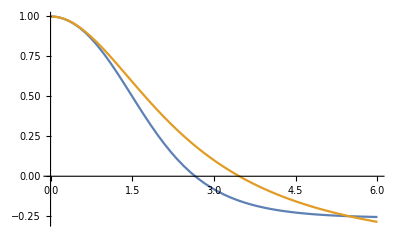

```mathematica
Plot[{(1 - h^2 / 12 - h^4/120) / (1 + h^2 / 6 + h^4/30), (1 - h^2 / 12) / (1 + h^2 / 6)}, {h, 0, 6}]
```